```mathematica
$Assumptions ={x∈Reals, y ∈ Reals, Subscript[t, 0] ∈ Reals,Subscript[t, 0] > 0,Subscript[t, 1] ∈ Reals, u ∈ Reals}
```

{x∈ℝ,y∈ℝ,t_0∈ℝ,t_0>0,t_1∈ℝ,u∈ℝ}

```mathematica
Subscript[σ, y] = {{0, -I}, {I, 0}}
Subscript[σ, x] = {{0, 1}, {1, 0}}
Subscript[σ, z] = {{1, 0}, {0, -1}}
```

{{0,-ⅈ},{ⅈ,0}}

{{0,1},{1,0}}

{{1,0},{0,-1}}

```mathematica
Subscript[f, k]=Exp[I y/Sqrt[3]] (1 + 2 Exp[-I y Sqrt[3]/2] Cos[1/2 x])
```

ⅇ^((ⅈ y)/(√3)) (1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2])

```mathematica
H0 = {{u, -Subscript[t, 0] Subscript[f, k]}, {-Subscript[t, 0] Conjugate[Subscript[f, k]], u}}
```

{{u,-ⅇ^((ⅈ y)/(√3)) (1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]) t_0},{-ⅇ^(-(ⅈ Conjugate[y])/(√3)) (1+2 ⅇ^(1/2 ⅈ √3 Conjugate[y]) Cos[Conjugate[x]/2]) t_0,u}}

```mathematica
FullSimplify[Normalize /@ Eigenvectors[H0]]
```

{{(ⅇ^((2 ⅈ y)/(√3)) (ⅇ^(1/2 ⅈ √3 y)+2 Cos[x/2]))/(√(ⅇ^((7 ⅈ y)/(2 √3)) (1+Abs[(2+ⅇ^(1/2 ⅈ √3 y) Sec[x/2])/(2 ⅇ^(1/2 ⅈ √3 y)+Sec[x/2])]) (2 (1+ⅇ^(ⅈ √3 y)) Cos[x/2]+ⅇ^(1/2 ⅈ √3 y) (3+2 Cos[x])))),1/(√(1+Abs[(2+ⅇ^(1/2 ⅈ √3 y) Sec[x/2])/(2 ⅇ^(1/2 ⅈ √3 y)+Sec[x/2])]))},{-(ⅇ^((2 ⅈ y)/(√3)) (ⅇ^(1/2 ⅈ √3 y)+2 Cos[x/2]))/(√(ⅇ^((7 ⅈ y)/(2 √3)) (1+Abs[(2+ⅇ^(1/2 ⅈ √3 y) Sec[x/2])/(2 ⅇ^(1/2 ⅈ √3 y)+Sec[x/2])]) (2 (1+ⅇ^(ⅈ √3 y)) Cos[x/2]+ⅇ^(1/2 ⅈ √3 y) (3+2 Cos[x])))),1/(√(1+Abs[(2+ⅇ^(1/2 ⅈ √3 y) Sec[x/2])/(2 ⅇ^(1/2 ⅈ √3 y)+Sec[x/2])]))}}

```mathematica
FullSimplify[Eigenvalues[H0]]
```

{u-ⅇ^(-(5 ⅈ y)/(2 √3)) √(ⅇ^((5 ⅈ y)/(√3)) (3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2])) t_0,u+ⅇ^(-(5 ⅈ y)/(2 √3)) √(ⅇ^((5 ⅈ y)/(√3)) (3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2])) t_0}

```mathematica
Subscript[c, 1]=-Subscript[t, 1] Subscript[f, k]/(2 u Abs[Subscript[f, k]])
Subscript[c, 2]=-Subscript[t, 1] 1/(2 u + 2 Subscript[t, 0] Abs[Subscript[f, k]])Subscript[f, k]/Abs[Subscript[f, k]]
```

-(ⅇ^((ⅈ y)/(√3)+Im[y]/(√3)) (1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]) t_1)/(2 u Abs[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]])

-(ⅇ^((ⅈ y)/(√3)+Im[y]/(√3)) (1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]) t_1)/(Abs[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]] (2 u+2 ⅇ^(-Im[y]/(√3)) Abs[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]] t_0))

```mathematica
FullSimplify[-Subscript[t, 1] Conjugate[Subscript[f, k]]/(2 Abs[Subscript[f, k]]) Subscript[c, 1] + -Subscript[t, 1] Conjugate[Subscript[f, k]]/(2 Abs[Subscript[f, k]])Subscript[c, 2] + -Subscript[t, 1] Subscript[f, k]/(2 Abs[Subscript[f, k]])Conjugate[Subscript[c, 1]] + -Subscript[t, 1] Subscript[f, k]/(2 Abs[Subscript[f, k]]) Conjugate[Subscript[c, 2]]]
```

(ⅇ^(-1/2 ⅈ √3 y) (ⅇ^(1/2 ⅈ √3 y)+2 Cos[x/2]) (1+2 ⅇ^(1/2 ⅈ √3 y) Cos[x/2]) (2 u+Abs[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]] t_0) t_1^2)/(2 u Abs[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]]^2 (u+Abs[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]] t_0))

```mathematica
FullSimplify[(ⅇ^(-1/2 ⅈ √3 y) (ⅇ^(1/2 ⅈ √3 y)+2 Cos[x/2]) (1+2 ⅇ^(1/2 ⅈ √3 y) Cos[x/2]) (2 u+Sqrt[(1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2])*Conjugate[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]]] Subscript[t, 0]) Subscript[t, 1]^2)/(2 u (1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2])Conjugate[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]] (u+Sqrt[Conjugate[1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2]]*(1+2 ⅇ^(-1/2 ⅈ √3 y) Cos[x/2])] Subscript[t, 0]))]
```

((2 u+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) t_0) t_1^2)/(2 u (u+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) t_0))

```mathematica
FullSimplify[((2 u+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) Subscript[t, 0]) Subscript[t, 1]^2)/(2 u (u+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) Subscript[t, 0])) +( u*(Subscript[N, L]+1)/2+Subscript[t, 0] Sqrt[Subscript[f, k]*Conjugate[Subscript[f, k]]])]
```

1/2 (u N_L+(u^3+2 u (3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) t_0^2+2 u t_1^2+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) t_0 (3 u^2+t_1^2))/(u (u+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) t_0)))

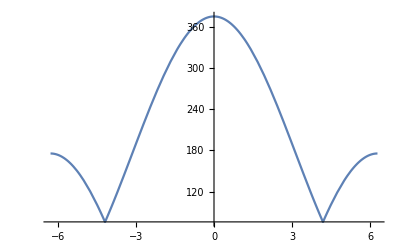

```mathematica
Plot[151/2+100 Abs[1+2 Cos[x/2]]+(1+50 Abs[1+2 Cos[x/2]])/(10000000000000000 (1+100 Abs[1+2 Cos[x/2]])),{x,-2 π,2 π}]
```

```mathematica
y = 0
u = 1
Subscript[N, L]=150
Subscript[t, 0]=100
Subscript[t, 1]=10
```

0

1

150

100

10

```mathematica
FullSimplify[1/2 (u Subscript[N, L]+(u^3+2 u (3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) Subscript[t, 0]^2+2 u Subscript[t, 1]^2+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) Subscript[t, 0] (3 u^2+Subscript[t, 1]^2))/(u (u+√(3+2 Cos[x]+4 Cos[x/2] Cos[(√3 y)/2]) Subscript[t, 0])))]
```

(60351+25300 Abs[1+2 Cos[x/2]]+80000 Cos[x/2]+40000 Cos[x])/(2+200 Abs[1+2 Cos[x/2]])

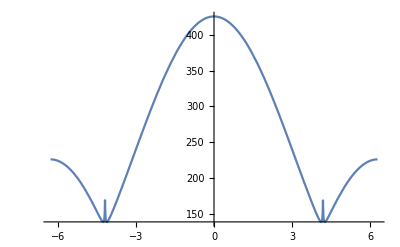

```mathematica
Plot[(60351+25300 Abs[1+2 Cos[x/2]]+80000 Cos[x/2]+40000 Cos[x])/(2+200 Abs[1+2 Cos[x/2]]),{x,-2 π,2 π}]
```